```mathematica
i10={{10.600,10.000,{42.31,0.68}},{10.740,10.000,{44.34,0.67}},{10.880,10.000,{46.28,0.75}},{11.020,10.000,{47.26,0.76}},{11.160,10.000,{50.13,0.83}},{11.300,10.000,{50.60,0.81}},{11.440,10.000,{52.72,0.88}},{11.580,10.000,{55.19,0.91}},{11.720,10.000,{57.62,0.97}},{11.860,10.000,{56.97,1.01}},{12.000,10.000,{61.09,1.04}}};
```

```mathematica
SolveNi[ii_]:=Module[{nc,data,weights,lf,a,b,c,ni,grad,err,foo},
nc=Min[ii[[All,2]]];
Assert[nc==Max[ii[[All,2]]]];
data={#[[1]],#[[3,1]]}&/@ii;
weights=1/(#[[3,2]])^2&/@ii;
lf=LinearModelFit[data,x,x,Weights->weights];
{a,b}=lf["BestFitParameters"];
c=lf["CovarianceMatrix"];
ni=(50-a)/b;
grad={-1/b,(a-50)/b^2};
err=Sqrt[grad.c.grad];
Print[Show[
ListPlot[{#[[1]],Around[#[[3,1]],#[[3,2]]]}&/@ii,AxesLabel->{"Ni","Ions"},
PlotLabel->StringTemplate["Nc = `1`, Ni = `2` ± `3`"][nc,ni,err]],
Plot[lf[x],{x,Min[ii[[All,1]]-1],Max[ii[[All,1]]+1]},PlotStyle->Orange],
Epilog->{PlotStyle->Black,Arrow[{{ni,60},{ni,51}}],Line[{{ni-err,50},{ni+err,50}}]}
]];
{nc,Around[ni,err]}
]
```

```mathematica
SolveNc[ii_]:=Module[{nc,data,weights,lf,a,b,c,ni,grad,err,foo},
ni=Min[ii[[All,1]]];
Assert[ni==Max[ii[[All,1]]]];
data={#[[2]],#[[3,1]]}&/@ii;
weights=1/(#[[3,2]])^2&/@ii;
lf=LinearModelFit[data,x,x,Weights->weights];
{a,b}=lf["BestFitParameters"];
c=lf["CovarianceMatrix"];
nc=(50-a)/b;
grad={-1/b,(a-50)/b^2};
err=Sqrt[grad.c.grad];
Print[Show[
ListPlot[{#[[2]],Around[#[[3,1]],#[[3,2]]]}&/@ii,AxesLabel->{"Nc","Ions"},
PlotLabel->StringTemplate["Ni = `1`, Nc = `2` ± `3`"][ni,nc,err]],
Plot[lf[x],{x,Min[ii[[All,2]]-1],Max[ii[[All,2]]+1]},PlotStyle->Orange],
Epilog->{PlotStyle->Black,Arrow[{{nc,60},{nc,51}}],Line[{{nc-err,50},{nc+err,50}}]}
]];
{Around[nc,err],ni}
]
```

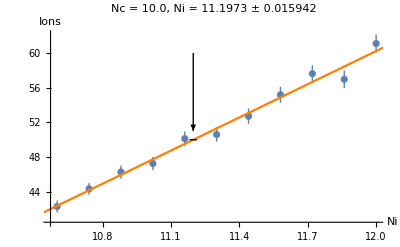

{10.,11.1970.016}

```mathematica
SolveNi[i10]
```

```mathematica
i10a={{10.500,10.000,{40.15,0.63}},{10.650,10.000,{42.80,0.65}},{10.800,10.000,{43.74,0.69}},{10.950,10.000,{45.34,0.71}},{11.100,10.000,{48.42,0.77}},{11.250,10.000,{50.02,0.82}},{11.400,10.000,{51.78,0.87}},{11.550,10.000,{53.95,0.93}},{11.700,10.000,{55.20,0.92}},{11.850,10.000,{58.40,1.00}},{12.000,10.000,{60.31,1.07}}};
```

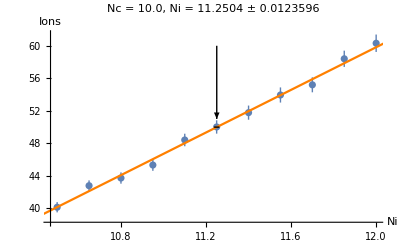

{10.,11.2500.012}

```mathematica
SolveNi[i10a]
```

```mathematica
i10b={{10.500,10.000,{40.32,0.61}},{10.650,10.000,{42.52,0.68}},{10.800,10.000,{44.35,0.70}},{10.950,10.000,{45.42,0.72}},{11.100,10.000,{47.62,0.77}},{11.250,10.000,{50.58,0.82}},{11.400,10.000,{52.72,0.87}},{11.550,10.000,{54.73,0.87}},{11.700,10.000,{56.00,0.94}},{11.850,10.000,{58.75,1.01}},{12.000,10.000,{60.52,1.03}}};
```

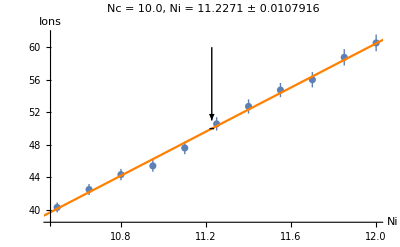

{10.,11.2270.011}

```mathematica
SolveNi[i10b]
```

```mathematica
i10c={{10.500,10.000,{39.65,0.59}},{10.650,10.000,{42.32,0.67}},{10.800,10.000,{45.08,0.68}},{10.950,10.000,{45.93,0.75}},{11.100,10.000,{46.65,0.76}},{11.250,10.000,{51.38,0.83}},{11.400,10.000,{52.72,0.89}},{11.550,10.000,{55.55,0.90}},{11.700,10.000,{55.37,0.94}},{11.850,10.000,{57.18,0.98}},{12.000,10.000,{60.56,1.07}}};
```

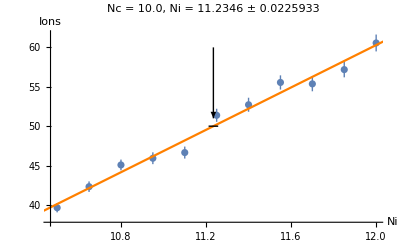

{10.,11.2350.023}

```mathematica
SolveNi[i10c]
```

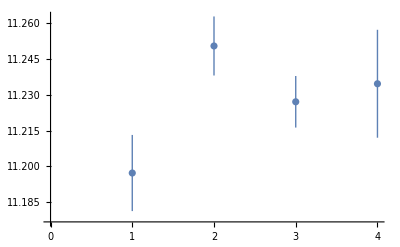

```mathematica
ListPlot[{11.1970.016,11.2500.012,11.2270.011,11.2350.023}]
```

```mathematica
StandardDeviation[#[[1]]&/@{11.1970.016,11.2500.012,11.2270.011,11.2350.023}]
```

0.0223038

```mathematica
Mean[{11.1970.016,11.2500.012,11.2270.011,11.2350.023}]
```

11.2270.008

```mathematica
paschenCurve={{10,%}}
```

{{10,11.2270.008}}

```mathematica
10^(1/4)//N
```

1.77828

```mathematica
10^(1/2)//N
```

3.16228

```mathematica
10^(3/4)//N
```

5.62341

```mathematica
i17={{10.500,17.800,{40.42,0.43}},{10.600,17.800,{41.11,0.44}},{10.700,17.800,{42.85,0.47}},{10.800,17.800,{45.43,0.49}},{10.900,17.800,{47.08,0.53}},{11.000,17.800,{49.55,0.55}},{11.100,17.800,{51.19,0.59}},{11.200,17.800,{53.55,0.63}},{11.300,17.800,{56.35,0.65}},{11.400,17.800,{57.41,0.67}},{11.500,17.800,{59.47,0.72}}};
```

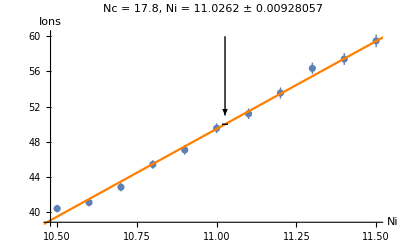

{17.8,11.0260.009}

```mathematica
SolveNi[i17]
```

```mathematica
i31={{12.200,31.600,{40.50,0.38}},{12.300,31.600,{42.72,0.42}},{12.400,31.600,{44.39,0.44}},{12.500,31.600,{46.45,0.45}},{12.600,31.600,{49.07,0.50}},{12.700,31.600,{51.68,0.50}},{12.800,31.600,{52.99,0.51}},{12.900,31.600,{55.78,0.53}},{13.000,31.600,{57.76,0.56}},{13.100,31.600,{61.34,0.58}},{13.200,31.600,{63.22,0.63}}};
```

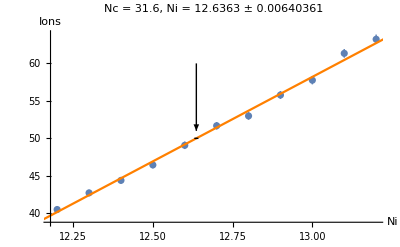

{31.6,12.6360.006}

```mathematica
SolveNi[i31]
```

```mathematica
i56={{15.000,56.200,{37.68,1.33}},{15.100,56.200,{41.29,1.00}},{15.200,56.200,{42.95,1.30}},{15.300,56.200,{42.84,1.39}},{15.400,56.200,{46.17,1.64}},{15.500,56.200,{48.98,1.46}},{15.600,56.200,{51.11,1.60}},{15.700,56.200,{53.34,1.63}},{15.800,56.200,{54.30,1.45}},{15.900,56.200,{55.89,1.72}},{16.000,56.200,{63.02,2.28}}};
```

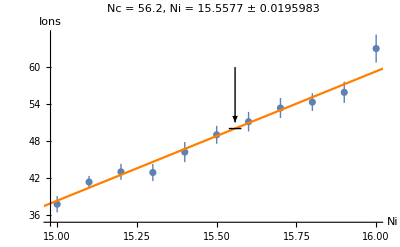

{56.2,15.5580.020}

```mathematica
SolveNi[i56]
```

```mathematica
i100={{20.000,100.000,{42.46,1.74}},{20.080,100.000,{46.70,1.64}},{20.160,100.000,{45.21,1.67}},{20.240,100.000,{47.63,1.77}},{20.320,100.000,{50.14,1.85}},{20.400,100.000,{50.92,1.73}},{20.480,100.000,{51.94,1.86}},{20.560,100.000,{51.26,1.86}},{20.640,100.000,{54.84,1.90}},{20.720,100.000,{59.09,2.09}},{20.800,100.000,{61.71,2.21}}}
```

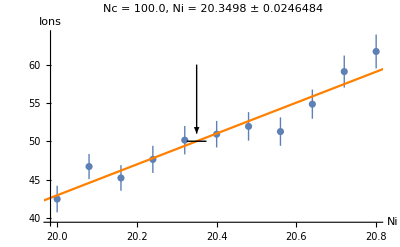

{100.,20.3500.025}

```mathematica
SolveNi[i100]
```

```mathematica
AppendTo[paschenCurve,%]
```

{{10,11.2270.008},{17.8,11.0260.009},{31.6,12.6360.006},{56.2,15.5580.020},{100.,20.3500.025}}

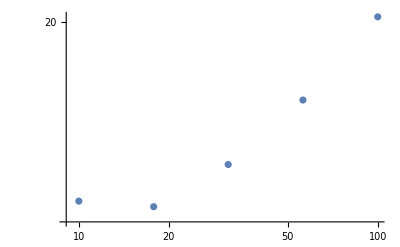

```mathematica
ListLogLogPlot[paschenCurve]
```

```mathematica
c20={{20.000,5.100,{38.77,1.00}},{20.000,5.170,{43.11,1.15}},{20.000,5.240,{46.82,1.26}},{20.000,5.310,{44.31,1.21}},{20.000,5.380,{48.58,1.29}},{20.000,5.450,{48.92,1.31}},{20.000,5.520,{50.99,1.34}},{20.000,5.590,{54.03,1.42}},{20.000,5.660,{55.08,1.36}},{20.000,5.730,{56.85,1.45}},{20.000,5.800,{57.90,1.51}}};
```

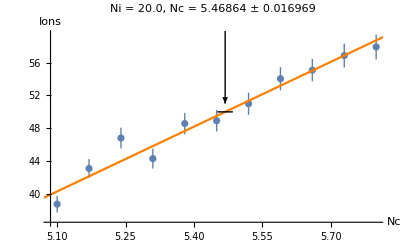

{5.4690.017,20.}

```mathematica
SolveNc[c20]
```

```mathematica
c15={{15.000,6.000,{42.47,1.03}},{15.000,6.100,{43.03,1.05}},{15.000,6.200,{46.27,1.08}},{15.000,6.300,{45.91,1.04}},{15.000,6.400,{47.91,1.14}},{15.000,6.500,{49.66,1.16}},{15.000,6.600,{50.79,1.17}},{15.000,6.700,{52.53,1.22}},{15.000,6.800,{56.79,1.32}},{15.000,6.900,{56.19,1.31}},{15.000,7.000,{60.16,1.41}}};
```

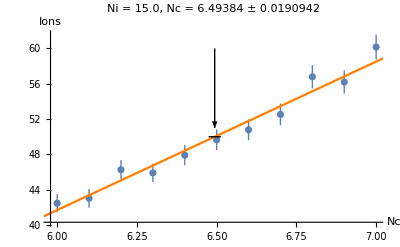

{6.4940.019,15.}

```mathematica
SolveNc[c15]
```

```mathematica
PrependTo[paschenCurve,%]
```

{{6.4940.019,15.},{5.4690.017,20.},{10,11.2270.008},{17.8,11.0260.009},{31.6,12.6360.006},{56.2,15.5580.020},{100.,20.3500.025}}

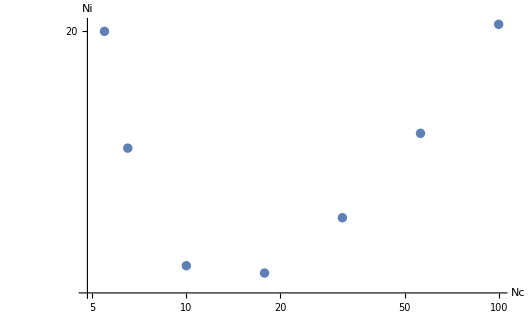

```mathematica
ListLogLogPlot[paschenCurve,AxesLabel->{"Nc","Ni"}]
```

```mathematica
Sort[paschenCurve,#1[[1]]<#2[[1]]&]
```

{{6.4940.019,15.},{5.4690.017,20.},{10,11.2270.008},{17.8,11.0260.009},{31.6,12.6360.006},{56.2,15.5580.020},{100.,20.3500.025}}